### Initialization of global variables and importing important structures

```mathematica
(* SET HERE THE WORKING DIRECTORY *)
SetDirectory["/u/16/heikkie13/unix/howard_scratches/Mathematica"];
<<libs/FunctionsComplexAnalysis.m;
<<libs/FunctionsMatrixAnalysis.m;
<<libs/FunctionsFiniteGroups.m;
<<libs/FunctionsGF2.m
<<libs/FunctionsForExtraSpeciality.m;

(* This is needed for the unitary reps of symplectivc matrices: *)
(* <<"SymplecticBinary.m"; *)

(*Clear[AllBinMats];*)
dB = 10*Log[10,N[#]]&;
Clear[mm,rr];
```

These are real variables:

{a,a_n_,b,b_n_,x,x_n_,y,y_n_,x̂,(x̂)_n_,ŷ,(ŷ)_n_,r,r_n_,s,s_n_,q,q_n_,p,p_n_,ϕ,ϕ_n_,φ,φ_n_,θ,θ_n_,ϑ,ϑ_n_,χ,χ_n_,ψ,ψ_n_,ζ,ζ_n_,ρ,ρ_n_,ϱ,ϱ_n_,η,η_n_,m,n,k,l,t,f,T}

These are specifically complex variables:

{h_n,(h_n)^*,((ĥ)_n)^*,(ĥ)_n,g_n,(g_n)^*,((ĝ)_n)^*,(ĝ)_n,n_p,(n_p)^*,((n̂)_p)^*,(n̂)_p,z_n,(z_n)^*,z,z^*,w_n,(w_n)^*,w,w^*,μ_n,(μ_n)^*,ν_n,(ν_n)^*,α,α^*,β,β^*,ν,ν^*,μ,μ^*,κ,κ^*,λ,λ^*}

Note that any variable which  is not specifically real, can be expressed with *. Conjugations do not work on these, but destar does.

```mathematica
(* These are needed for functions to work properly *)
(* The dimension for the simulation must be chosen here, as multiple data structures neede by decoders etc depend on m*)
mm = 3; Nn= 2^mm; InxBin= Tuples[{0,1},{mm}]; WHn = WHmatrix[Nn]/Sqrt[Nn];  InitializeVeryBare[mm];
ZeroVecm = Table[0,{mm}];
PermMatEShifts = TensorMany[Join[Table[unit2,{#}],{sigx},Table[unit2,{mm-1-#}]]] &/@ (Range[mm]-1); PermMatEShifts //mfl
```

{(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

### Codebook

```mathematica
GenerateChirp = Module[{Sint, bvec,xvec},Sint = #1; bvec = #2;
(xvec  = IntegerDigits[#-1,2,mm];
I^(xvec.Sint.xvec + 2 bvec.xvec)/Sqrt[2^mm]) &/@ Range[2^mm]
]&;

MakeUnitaryFromSymmetric = Module[{Sint,cvec,dvec,Ord2},Sint = #;
 (cvec = IntegerDigits[#-1,2,mm];
Ord2 = cvec.Sint.cvec;
(dvec  = IntegerDigits[#-1,2,mm];
I^(Ord2 + 2 dvec.cvec)/Sqrt[2^mm]
) &/@ Range[2^mm]
) &/@ Range[2^mm] ]&; 

AllBinSymm = GenerateSn2[mm];
AllUmats = MakeUnitaryFromSymmetric[#] &/@ AllBinSymm;
AllUmats // mfl;
CB  = Transpose[Sequence@@(Transpose[#]) &/@ AllUmats]; card = Length[CB[[1]]]; {Length[AllUmats],card}
```

{64,512}

### Decoders

#### Extended decoder

```mathematica
ExtendedDecoder=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest},vecin=#;
squared=vecin*vecin;
squared=squared/Norm[squared];
{Sest, zleft, best, metric}=BreadthFirstDecoding[{squared, Range[mm], 1, True}];
MaskS=Sest/2;
MaskChirp= GenerateChirp[MaskS,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
{Sest, zleft, best, metric}=BreadthFirstDecoding[{UnmaskedChirp, Range[mm], 1, True}];
{Sest+MaskS,best}]&;
```

#### Truth table calculators and decoding order

```mathematica
DecodingOrder = Module[{vecin, maxis, PermMatEsh, abses, permutetable}, vecin = #;
maxis = {};
(inx = #;
	PermMatEsh =  PermMatEShifts[[inx]];
	abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn];
	maxis  = Append[maxis, Max[abses]];
) &/@ Range[mm];
Reverse[Ordering[maxis]]
]&;

GiveTruthTable = Module[{index, size, basetable, binary}, input=#;
index = #[[1]];
size = #[[2]];
binary = Mod[Floor[(Range[2^size] - 1) / 2^(size -index)], 2];
Table[binary[[i]] == 0, {i, 1, 2^size}]
]&;

UpdateTruthTable = Module[{tt1, tt2}, input = #;
tt1 = #[[1]];
tt2 = #[[2]];
Table[tt1[[i]] && tt2[[i]], {i, 1, Length[tt1]}]
]&;
```

#### Row decoders

```mathematica
DecodeRowList = Module[{vecin, mu, Sest, signbits, tt, r, K, start, RangeNow, newK, wht, abses, signs, metrics, signbitsall, projectedvectors, Sests, peaks, peak, Sestk, metrick , k, PhaseVec, sigmak, signbitsk, Svec, avec, bvec, X, vecrot, veck, results, PermMatEsh, peaki, withProjections}, 
Sest = #[[1]];
vecin = #[[2]];
signbits = #[[3]];
mu = #[[4]];
tt = #[[5]];
r = #[[6]];
K = #[[7]];
withProjections = #[[8]];

start = Transpose[Sest][[r]];
RangeNow=Pick[Range[2^mm],tt] + FromDigits[start,2];

(* In the end K might be greater than the number of possible different rows *)
newK = Min[K, Length[RangeNow]];

avec = ZeroVecm; avec[[r]]=1;
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(-avec.bvec)) &/@ Range[Nn];

PermMatEsh =  PermMatEShifts[[r]];
wht =  Sqrt[Nn]PhaseVec*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn;
abses = Abs[wht];
signs = Sign[Re[wht]];

metrics = {};
signbitsall = {};
projectedvectors = {};
Sests = {};


peaks = Reverse[Sort[abses[[RangeNow]]]];
results = {};
(k=#;
peaki = Position[abses,peaks[[k]]][[1,1]];
(* peak = peaks[[k]]; *)
(* Mathematica copies arrays by default so no worries of reference problems *)
Sestk = Sest;

If[withProjections, metrick = (mu + abses[[peaki]]) / 2;, metrick = (mu + abses[[peaki]]);];
(* May give wrong result *)
sigmak = signs[[peaki]];

signbitsk = signbits; 
signbitsk[[r]] =(1 - sigmak) / 2;

Svec  = IntegerDigits[peaki-1,2,mm];
Sestk[[r]]=Svec;


If[withProjections, avec = ZeroVecm; avec[[r]]=1;
(* construct the  Pauli found, the sought for codeword is an eigenvector of this Pauli with eigenvalue +- 1  *)
X = MakePauli[avec,Svec];
vecrot = X.vecin;
veck = (vecin + sigmak * vecrot) / 2;, 
(* This runs if withProjections = False *)
veck = vecin;];

results = Append[results, {Sestk, veck, signbitsk, metrick}];
) &/@ Range[newK];
results
]&;
```

#### List decoder

```mathematica
BreadthFirstDecoding = Module[{vecin, ordering, tt, Sest, K, candidatelist, newcandidates, r, inx, jnx, metrics, peakinxs, withProjections}, vecin = #[[1]]; ordering = #[[2]]; K = #[[3]];withProjections = #[[4]];
tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
candidatelist = {{Table[0,{mm},{mm}], vecin, Table[0, mm], Norm[vecin]^2}};
(inx = #;
newcandidates = {};
r = ordering[[inx]];
(jnx = #;
(* FOR FUTURE DEVELOPEMENT: If ordering is modified during the run, this needs to be improved *)
newcandidates = Join[newcandidates,DecodeRowList[Join[candidatelist[[jnx]],{tt, r, K, withProjections}]]];
)&/@Range[Length[candidatelist]];
metrics = {};
(* TODO optimize *)
(jnx = #; metrics = Append[metrics, newcandidates[[jnx,4]]];) &/@Range[Length[newcandidates]];
peakinxs = Reverse[Ordering[metrics]];
candidatelist = {};
(* TODO optimize *)
(jnx = #; candidatelist = Append[candidatelist, newcandidates[[peakinxs[[jnx]]]]];)&/@Range[Min[K, Length[newcandidates]]];
tt = UpdateTruthTable[{GiveTruthTable[{r, mm}], tt}];
)&/@ Range[mm];


If[withProjections, posi = 1, inners = (best = #[[3]]; best = 1 - best; Sest = #[[1]];
vecest = (cvec = IntegerDigits[#-1,2,mm];(-I)^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Abs[Conjugate[tstvec].vecest]
) &/@ candidatelist;

posi = Position[inners,Max[inners]][[1,1]]; ];
candidatelist[[posi]]
]&;
```

### Simulation

```mathematica
Smat = {{0,1,1}, {1,0,0}, {1,0,1}}; Smat //mf
bvec = {0,1,0}; bvec//mf
tstvec = GenerateChirp[Smat, bvec];
```

(0 | 1 | 1
1 | 0 | 0
1 | 0 | 1)

(0
1
0)

```mathematica
{Sest, zleft, best, metric} = BreadthFirstDecoding[{tstvec, Range[mm], 1, False}];
vecest = Conjugate[GenerateChirp[Sest, bvec]];
Sest // mf
```

(0 | 1 | 1
1 | 0 | 0
1 | 0 | 1)

```mathematica
If[Abs[tstvec.vecest]> 0.99,1,0]
```

1

```mathematica
bvec // mf
```

(0
1
0)

```mathematica
Total[{0,1,0}]
```

1

```mathematica
(* Creates upper triangular matrix from vector *)
upperTriangular[v_]:=upperTriangular[v,(1+Sqrt[1+8*Length@v])/2]
upperTriangular[v_,n_]:=Module[{i=0},Array[If[#>=#2,0,v[[++i]]]&,{n,n}]]
upperTriangulizer[n_Integer,type_:_Integer]:=Module[{v,r},Quiet[With[{r=upperTriangular[v,n]},Compile[{{v,type,1}},r]],Part::partd]]
(* Example printed below *)
upperTriangulizer[3] @ Range[3] // MatrixForm;
ExtendedSymmetricMats=Module[{size, diag, diagmat, triuvec, triumat, result, results, inx},size=#;
results={};
(inx=#;
diag=IntegerDigits[Mod[inx,2^size],2,size];
diagmat=DiagonalMatrix[diag];
triuvec=IntegerDigits[Floor[inx/(2^size)],4, (size - 1)*size / 2];
triumat=(upperTriangulizer[size]@triuvec)/2;
result=triumat+Transpose[triumat]+diagmat;
AppendTo[results,result];)&/@Range[0,2^(size^2)-1];
results
]&;
ExtendedSmats = ExtendedSymmetricMats[mm]; ExtendedSmats // mfl;
```

```mathematica
Smatrix=ExtendedSmats[[57]]; Smatrix // mf
bvec = {0,1,0};
chirp = GenerateChirp[Smatrix, bvec];
{Sestimate,bestimate}=ExtendedDecoder[chirp];
Sestimate // mf;
bestimate //mf;
(*
(Smatrix=#;
(bvector=IntegerDigits[#-1,2,mm];
chirp=GenerateChirp[Smatrix,bvector];
{Sestimate,bestimate}=ExtendedDecoder[chirp];
If[Union[Flatten[Sestimate-Smatrix]]!={0},Print["Decoder failed"]];
If[Union[bestimate-bvector]!={0},Print["Decoder failed"]];
)&/@Range[Nn]; )&/@ExtendedSmats; 
*)
(*
For practical purposes,we would have K>>1 codewords sent simultaneously,and then some noise.You could model the channel as



y=sqrt[N*gamma]*(sum_{i=1}^K w_i)+noise,where w_i are codewords in N dimensions,noise=(randn(N,1)+1i*randn(N,1))/sqrt[2],and gamma is real number (SNR=10*log10[gamma],so,for instance,gamma=100 gives SNR=20,gamma=10 gives SNR=10 etc) that controls the power.
*)
```

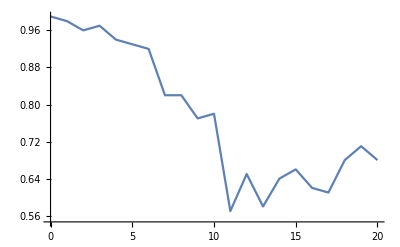

e5

```mathematica
drops = 100;
SNRValues = Range[0,20,1];
Results = {};
(SNR = #;
gamma = 10^(SNR/10);
errors = 0;
(
Smatrix = RandomChoice[ExtendedSmats];
bvector = RandomChoice[{0,1}, mm];
chirp = GenerateChirp[Smatrix, bvector];
tstvec = Sqrt[Nn*gamma]*chirp + {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]/Sqrt[2];
{Sestimate,bestimate}=ExtendedDecoder[tstvec];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors += 1];
)&/@ Range[drops];
AppendTo[Results, {SNR, errors/drops//N}];
)&/@ SNRValues;
ListLinePlot[Results]
```

```mathematica
RandomVariate[NormalDistribution[], Nn]
```

{-0.920283,-0.226194,-0.250147,0.986777,1.99819,-0.432657,0.917166,-0.267559}

```mathematica
RandomChoice[{0,1}, 10] //mf
```

(0
0
0
0
0
1
1
1
1
0)

4096

```mathematica
True || False
```

True

{0.57689+0.702202 ⅈ,0.677111+0.156661 ⅈ,-0.335343-0.855819 ⅈ,0.0302393-0.0698888 ⅈ,0.676112-0.40409 ⅈ,0.147488-0.245306 ⅈ,-0.363191-0.707943 ⅈ,-0.10132-0.557053 ⅈ}

10**0.3247